```mathematica
Pars ={r1->5/7,r2->1,a11->1,a12->9/5,a21->2/3,a22->1,c11->1,c12->6/7,c21->1,c22->1,v->3/4,a13->1/2,a23->1/2,e1->1/2,e2->1/2};
System={N1'[t]==r1*N1[t](1+a11*M1[t]+a12*M2[t]+a13*(1-M1[t]-M2[t]))-c11*(N1[t])^2-c12*N1[t]*N2[t],
N2'[t]==r2*N2[t](1+a21 *M1[t]+a22*M2[t]+a23(1-M1[t]-M2[t]))-c22*(N2[t])^2-c21*N1[t]*N2[t],
M1'[t]==(M1[t]*M2[t])/(N1[t]+N2[t])(N1[t]-v*N2[t])-M1[t]*(1-M1[t]-M2[t])/(N1[t]+N2[t])(e1*N1[t]+e2*N2[t]),
M2'[t]==(M1[t]*M2[t])/(N1[t]+N2[t])(v *N2[t]-N1[t])-M2[t]*(1-M1[t]-M2[t])/(N1[t]+N2[t])(e1*N1[t]+e2*N2[t])}/.Pars
```

{N1'[t]==5/7 (1+M1[t]+1/2 (1-M1[t]-M2[t])+(9 M2[t])/5) N1[t]-N1[t]^2-6/7 N1[t] N2[t],N2'[t]==(1+(2 M1[t])/3+1/2 (1-M1[t]-M2[t])+M2[t]) N2[t]-N1[t] N2[t]-N2[t]^2,M1'[t]==(M1[t] M2[t] (N1[t]-(3 N2[t])/4))/(N1[t]+N2[t])-(M1[t] (1-M1[t]-M2[t]) (N1[t]/2+N2[t]/2))/(N1[t]+N2[t]),M2'[t]==-((1-M1[t]-M2[t]) M2[t] (N1[t]/2+N2[t]/2))/(N1[t]+N2[t])+(M1[t] M2[t] (-N1[t]+(3 N2[t])/4))/(N1[t]+N2[t])}

```mathematica
Fps = FullSimplify[Solve[{r1*N1(1+a11*M1+a12*M2+a13*(1-M1-M2))-c11*(N1)^2-c12*N1*N2 == 0, r2*N2(1+a21 *M1+a22*M2+a23(1-M1-M2))-c22*(N2)^2-c21*N1*N2==0, (M1*M2)/(N1+N2)(N1-v*N2)-M1*(1-M1-M2)/(N1+N2)(e1*N1+e2*N2) == 0, (M1*M2)/(N1+N2)(v *N2-N1)-M2*(1-M1-M2)/(N1+N2)(e1*N1+e2*N2)==0}/. Pars, {N1, N2, M1, M2}]]
```

{{N1→-3/2,N2→3,M1→0,M2→0},{N1→0,N2→23/18,M1→2/3,M2→-2/3},{N1→0,N2→3/2,M1→0,M2→0},{N1→0,N2→5/3,M1→1,M2→0},{N1→0,N2→2,M1→0,M2→1},{N1→10/13,N2→40/39,M1→8/13,M2→5/13},{N1→15/14,N2→0,M1→0,M2→0},{N1→2,N2→0,M1→0,M2→1},{N1→1/78 (-23-2 √3613),N2→1/234 (467+5 √3613),M1→1/78 (-47+√3613),M2→1/78 (47-√3613)},{N1→1/78 (-23+2 √3613),N2→1/234 (467-5 √3613),M1→1/78 (-47-√3613),M2→1/78 (47+√3613)},{N1→19/14,N2→0,M1→-1/2,M2→1/2},{N1→10/7,N2→0,M1→1,M2→0},{N1→2,N2→0,M1→0,M2→1}}

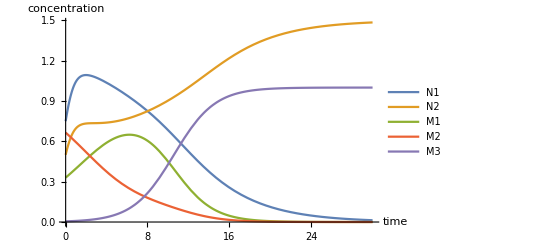

```mathematica
s=NDSolve[Union[System, {N1[0]==3/4, N2[0]==1/2, M1[0]==0.33, M2[0]==0.665}], {N1, N2, M1, M2}, {t, 0, 1000}];
Plot[Evaluate[{N1[t], N2[t], M1[t], M2[t], 1- M1[t] - M2[t]}/. s], {t,0,30},PlotRange -> All, PlotLegends->{"N1", "N2", "M1", "M2", "M3"},AxesLabel->{"time", "concentration"}]
```

```mathematica
Pars ={r1->5/7,r2->1,a11->1,a12->9/5,a21->2/3,a22->1,c11->1,c12->6/7,c21->1,c22->1,v->3/4,a13->0,a23->0,e1->0,e2->0};
System={N1'[t]==r1*N1[t](1+a11*M1[t]+a12*M2[t]+a13*(1-M1[t]-M2[t]))-c11*(N1[t])^2-c12*N1[t]*N2[t],
N2'[t]==r2*N2[t](1+a21 *M1[t]+a22*M2[t]+a23(1-M1[t]-M2[t]))-c22*(N2[t])^2-c21*N1[t]*N2[t],
M1'[t]==(M1[t]*M2[t])/(N1[t]+N2[t])(N1[t]-v*N2[t])-M1[t]*(1-M1[t]-M2[t])/(N1[t]+N2[t])(e1*N1[t]+e2*N2[t]),
M2'[t]==(M1[t]*M2[t])/(N1[t]+N2[t])(v *N2[t]-N1[t])-M2[t]*(1-M1[t]-M2[t])/(N1[t]+N2[t])(e1*N1[t]+e2*N2[t])}/.Pars
```

{N1'[t]==5/7 (1+M1[t]+(9 M2[t])/5) N1[t]-N1[t]^2-6/7 N1[t] N2[t],N2'[t]==(1+(2 M1[t])/3+M2[t]) N2[t]-N1[t] N2[t]-N2[t]^2,M1'[t]==(M1[t] M2[t] (N1[t]-(3 N2[t])/4))/(N1[t]+N2[t]),M2'[t]==(M1[t] M2[t] (-N1[t]+(3 N2[t])/4))/(N1[t]+N2[t])}

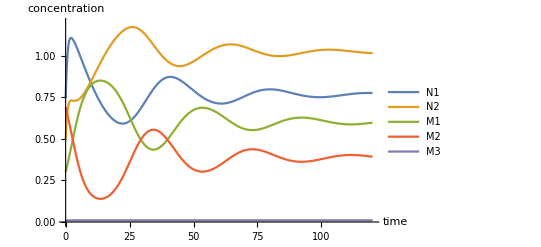

```mathematica
s=NDSolve[Union[System, {N1[0]==3/4, N2[0]==1/2, M1[0]==0.3, M2[0]==0.69}], {N1, N2, M1, M2}, {t, 0, 1000}];
Plot[Evaluate[{N1[t], N2[t], M1[t], M2[t], 1 - M1[t] - M2[t]}/. s], {t,0,120},PlotRange -> {0,1.2}, PlotLegends->{"N1", "N2", "M1", "M2", "M3"}, AxesLabel->{"time", "concentration"}]
```

```mathematica
Pars ={r1->5/7,r2->1,a11->1,a12->9/5,a21->2/3,a22->1,c11->1,c12->6/7,c21->1,c22->1,v->3/4};
InitialConditions={N1[0]==((a12+a21+a12 a21-a22-a11 (1+a22)) r1 r2 v)/((a21-a22) r2 (c12+c11 v)-a11 r1 (c22+c21 v)+a12 r1 (c22+c21 v)),N2[0]==((a12+a21+a12 a21-a22-a11 (1+a22)) r1 r2)/((a21-a22) r2 (c12+c11 v)-a11 r1 (c22+c21 v)+a12 r1 (c22+c21 v)),
M1[0]==((1+a12) c22 r1+(1+a12) c21 r1 v-(1+a22) r2 (c12+c11 v))/((a21-a22) r2 (c12+c11 v)-a11 r1 (c22+c21 v)+a12 r1 (c22+c21 v))-0.005,
M2[0]==(1-((1+a12) c22 r1+(1+a12) c21 r1 v-(1+a22) r2 (c12+c11 v))/((a21-a22) r2 (c12+c11 v)-a11 r1 (c22+c21 v)+a12 r1 (c22+c21 v)))-0.005}/.Pars
```

{N1[0]==10/13,N2[0]==40/39,M1[0]==0.610385,M2[0]==0.379615}

```mathematica
d = 1/8;
Pars ={r1->5/7,r2->1,a11->1,a12->9/5,a21->2/3,a22->1,c11->1,c12->6/7,c21->1,c22->1,v->3/4};
data = {{"a13","a23","e1", "e2", "N1_f", "N2_f", "M1_f","M2_f", "N1'_f", "N2'_f", "M1'_f", "M2'_f"}};
For[a13 =-2,a13<=2,a13+=d,
For[a23=-2,a23<=2,a23+=d,
For[e1=-2,e1<=2,e1+=d,
For[e2=-2,e2<=2,e2+=d,
System={N1'[t]==r1*N1[t](1+a11*M1[t]+a12*M2[t]+a13*(1-M1[t]-M2[t]))-c11*(N1[t])^2-c12*N1[t]*N2[t],
N2'[t]==r2*N2[t](1+a21 *M1[t]+a22*M2[t]+a23(1-M1[t]-M2[t]))-c22*(N2[t])^2-c21*N1[t]*N2[t],
M1'[t]==(M1[t]*M2[t])/(N1[t]+N2[t])(N1[t]-v*N2[t])-M1[t]*(1-M1[t]-M2[t])/(N1[t]+N2[t])(e1*N1[t]+e2*N2[t]),
M2'[t]==(M1[t]*M2[t])/(N1[t]+N2[t])(v *N2[t]-N1[t])-M2[t]*(1-M1[t]-M2[t])/(N1[t]+N2[t])(e1*N1[t]+e2*N2[t])}/.Pars;
Solution=NDSolve[Union[System,InitialConditions],{N1, N2,M1,M2},{t,0,1000}, Method ->"StiffnessSwitching"];
row = {N[a13],N[a23],N[e1],N[e2], First[N1[1000]/.Solution],First[N2[1000]/.Solution], First[M1[1000]/.Solution],First[M2[1000]/.Solution],First[N1'[1000]/.Solution],First[N2'[1000]/.Solution], First[M1'[1000]/.Solution], First[M2'[1000]/.Solution]};
AppendTo[data, row]]]]];
Export["3M_system_data.csv", data, "CSV"]
```

NDSolve::ndsz: At t == 83.1511, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 933.238, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 296.67, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

3M_system_data.csv